## Analysis functions

```mathematica
expFitRaw0B[Datalist_]:=Block[{fitData,tnlm,tparaInterval,tpars,tar,tcr},
fitData=Table[{2i-1,Datalist[[i]]},{i,Length[Datalist]}];
tnlm=NonlinearModelFit[fitData,{(-1)*Exp[a-b x]+c,a>0&&b>0},{a,{b,0.5},c},x,ConfidenceLevel->0.6827];
Quiet[tparaInterval=tnlm["ParameterConfidenceIntervals"]];
tpars=tnlm["BestFitParameters"];
tar=Around[tpars[[1,2]],{tparaInterval[[1,1]]-tpars[[1,2]],tparaInterval[[1,2]]-tpars[[1,2]]}];
tcr=Around[tpars[[3,2]],{tparaInterval[[3,1]]-tpars[[3,2]],tparaInterval[[3,2]]-tpars[[3,2]]}];
Return[{-Exp[tar],tcr}];];
InferEnergyExp0B[listAB_,Ebell_]:=(* slightly improved analysis*)Module[{a1,c1,a2,c2},{a1,c1}=expFitRaw0B[listAB[[1]]];{a2,c2}=expFitRaw0B[listAB[[2]]];a1*(Ebell-c2)/a2+c1];
```

## Washington 102 qubits; 40K; 25 repetitions; Δ=1

### Ansatz Energy

```mathematica
aveE={-119.94163031417962,-46.38149625632239,-23.232567651076494,-14.635224078975222,-13.027507628317336};
stdE={0.18947319495890055,0.12471761331012043,0.1373103816952494,0.11050957959609051,0.09003060836576429};
```

```mathematica
data=Table[{2*i-1,aveE[[i]]}, {i,1, Length[aveE]}]
```

{{1,-119.942},{3,-46.3815},{5,-23.2326},{7,-14.6352},{9,-13.0275}}

```mathematica
nlm=NonlinearModelFit[data,a Exp[-b x]+c,{a,b,c},x,ConfidenceLevel->0.6827]
```

FittedModel[-11.5817-190.862 ⅇ^(-0.566205 x)]

```mathematica
nlm[y]
```

-11.5817-190.862 ⅇ^(-0.566205 y)

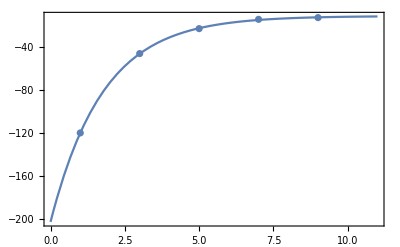

```mathematica
Show[ListPlot[data],Plot[nlm[x],{x,0,11},PlotRange->All],Frame->True,PlotRange->All]
```

```mathematica
nlm["ParameterConfidenceIntervals"]
```

{{-193.384,-188.34},{0.55297,0.57944},{-12.2035,-10.9599}}

#### Bell pairs energy

```mathematica
aveEB={-108.278778381602,-44.46938212945125,-24.892065384806912,-17.115442705443872,-13.757369654233147};
stdEB={0.1616230641511099,0.12289603661582321,0.14336452882656972,0.1407740732401406,0.1091808599525253};
```

```mathematica
dataB=Table[{2*i-1,aveEB[[i]]}, {i,1, Length[aveEB]}]
```

{{1,-108.279},{3,-44.4694},{5,-24.8921},{7,-17.1154},{9,-13.7574}}

```mathematica
nlm=NonlinearModelFit[dataB,a Exp[-b x]+c,{a,b,c},x,ConfidenceLevel->0.6827]
```

FittedModel[-13.2595-163.893 ⅇ^(-0.5462 x)]

```mathematica
nlm[y]
```

-13.2595-163.893 ⅇ^(-0.5462 y)

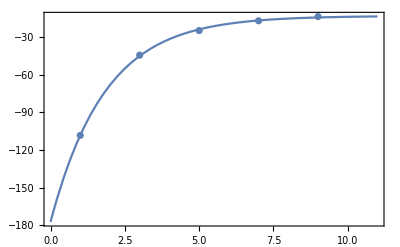

```mathematica
Show[ListPlot[dataB],Plot[nlm[x],{x,0,11},PlotRange->All],Frame->True,PlotRange->All]
```

#### Energy calibration by reference state

```mathematica
Δ=1;
(-2-Δ)*102/2
```

-153

```mathematica
InferEnergyExp0B[{aveE,aveEB},-153]
```

-174.5.5.

## Montreal 8 qubits; 32K; 10 repetitions; Δ=0.8

### Ansatz Energy

```mathematica
aveE={-9.659112196805905,-5.845587868290541,-3.286096526071532,-1.7431579126519228,-0.9074724869201791,-0.5155076109660939};
stdE={0.017830090747346934,0.011596526976656495,0.009148891451334374,0.006458284166729239,0.007125124757942715,0.0073685395684375534};
```

```mathematica
data=Table[{2*i-1,aveE[[i]]}, {i,1, Length[aveE]}]
```

{{1,-9.65911},{3,-5.84559},{5,-3.2861},{7,-1.74316},{9,-0.907472},{11,-0.515508}}

```mathematica
nlm=NonlinearModelFit[data,-a Exp[-b x]+c,{a,b,c},x,ConfidenceLevel->0.6827]
```

FittedModel[0.416581-12.9876 ⅇ^(-0.249649 x)]

```mathematica
nlm[y]
```

0.416581-12.9876 ⅇ^(-0.249649 y)

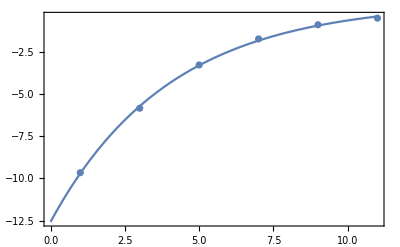

```mathematica
Show[ListPlot[data],Plot[nlm[x],{x,0,11},PlotRange->All],Frame->True,PlotRange->All]
```

```mathematica
nlm["ParameterConfidenceIntervals"]
```

{{12.7605,13.2148},{0.234755,0.264543},{0.188671,0.644491}}

#### Bell pairs energy

```mathematica
aveEB={-8.816268960487122,-5.727403558294131,-3.33543001013454,-1.6407210285754665,-0.993124116695107,-0.5829188984245655};
stdEB={0.011089926875818104,0.010545291859892069,0.01210860352764617,0.01299701603780817,0.007972924119289774,0.011722363139510404};
```

```mathematica
dataB=Table[{2*i-1,aveEB[[i]]}, {i,1, Length[aveEB]}]
```

{{1,-8.81627},{3,-5.7274},{5,-3.33543},{7,-1.64072},{9,-0.993124},{11,-0.582919}}

```mathematica
nlm=NonlinearModelFit[dataB,-a Exp[-b x]+c,{a,b,c},x,ConfidenceLevel->0.6827]
```

FittedModel[0.616864-11.8685 ⅇ^(-0.220557 x)]

```mathematica
nlm[y]
```

0.616864-11.8685 ⅇ^(-0.220557 y)

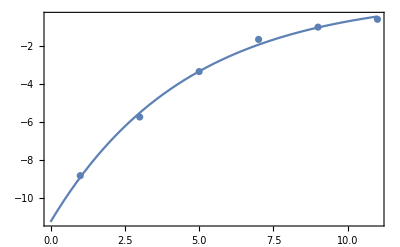

```mathematica
Show[ListPlot[dataB],Plot[nlm[x],{x,0,11},PlotRange->All],Frame->True,PlotRange->All]
```

#### Energy calibration by reference state

```mathematica
Δ=0.8;
(-2-Δ)*8/2
```

-11.2

```mathematica
InferEnergyExp0B[{aveE,aveEB},-11.2]
```

-12.50.90.9